# Time-Series Analysis

### Initializing Time-Series Data for the Sample

```mathematica
TimeSeriesData = ;
```

Month:				The month for which the data of the same row has been taken

Russell2000Returns:		The return of the Russell 2000 for the month

VIX:				The average of the CBOE Equity Volatility Index for the month

FederalFundsEffectiveRate:	The federal funds effective rate

FederalFundsTargetRate:	The upper limit of the federal funds target range on the first of the month

PutCallRatio:			The CBOE Equity Put/Call-Ratio on the first of the month

SPACReturn:			The average return of the SPAC sample for the month, taken from all deSPAC firms within the first year after the merger

SPACAR:			SPACReturn minus Russell2000Returns

TimePlotDate:			months numbered in order  to construct a time-plot

## Analysis of absolute returns

### Checking the pairwise scatterplot and correlation matrix for possible multi-colinearity and possible non-linear relationships

```mathematica
Needs["StatisticalPlots`"]
```

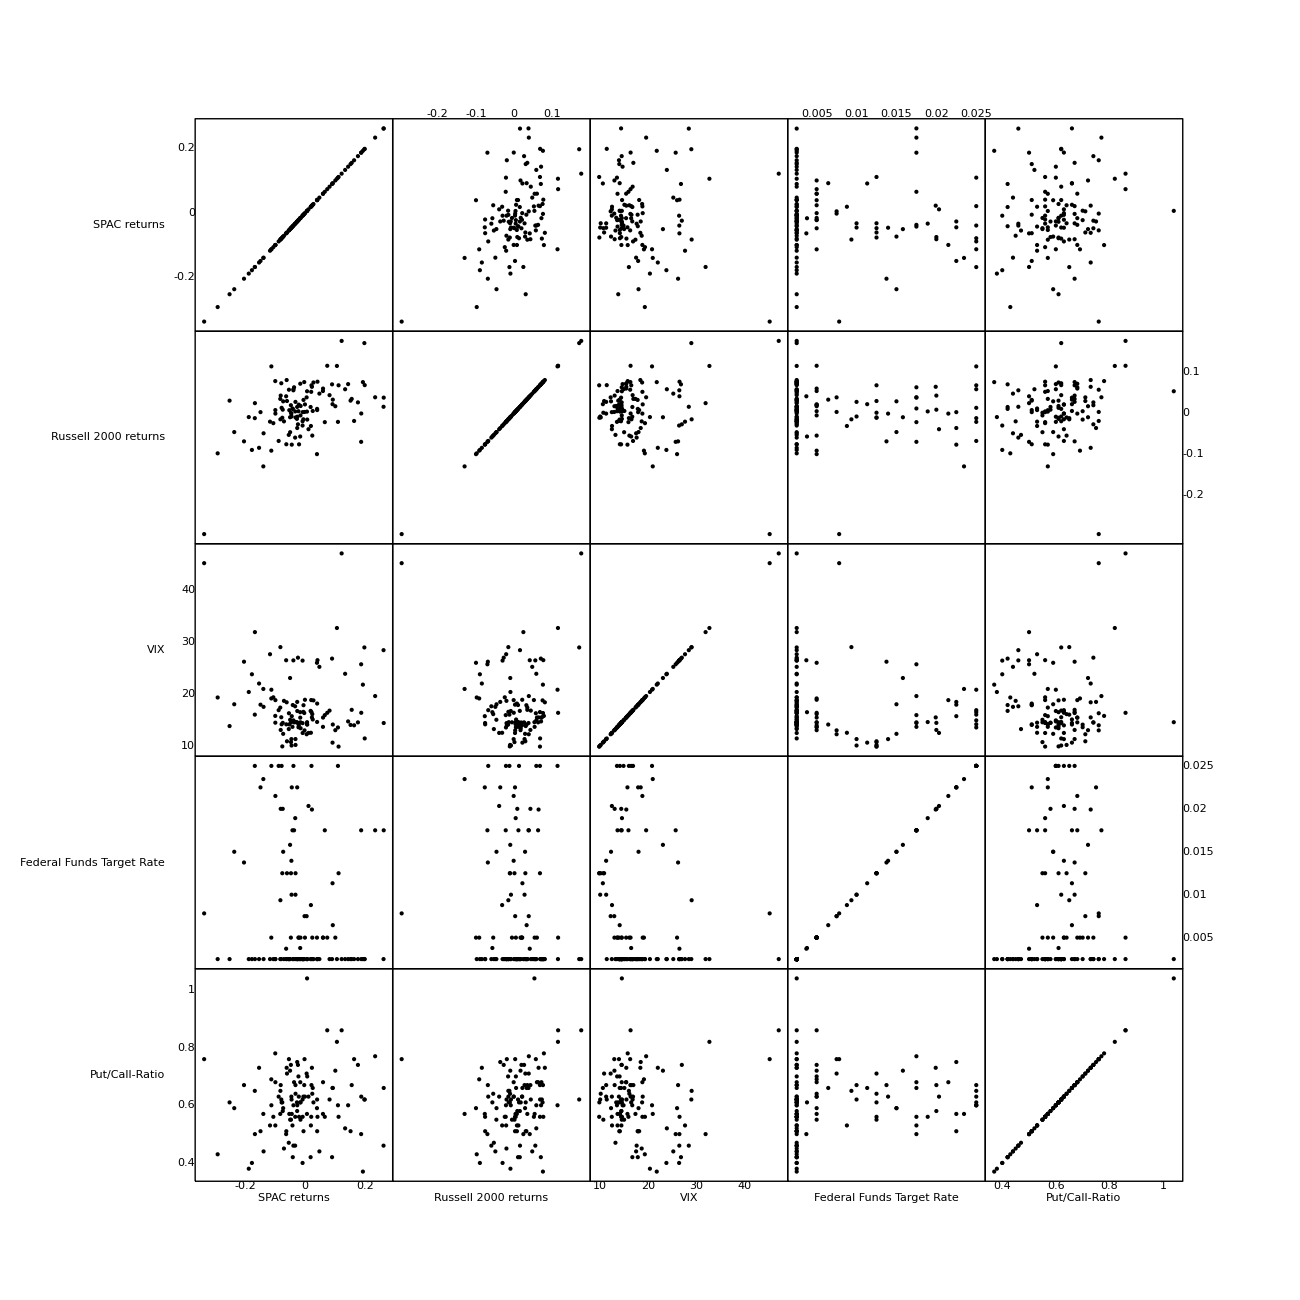

```mathematica
PairwiseScatterPlot[TimeSeriesData[#&, {#SPACReturn, #Russell2000Returns, #VIX, #FederalFundsTargetRate, #PutCallRatio}&]//Normal, DataLabels->{"SPAC returns", "Russell 2000 returns", "VIX", "Federal Funds Target Rate", "Put/Call-Ratio"}, DataTicks->True, ImageSize->1300]
```

There does not seem to be a strong relationship between any of the independent variable, which the correlation matrix also confirms. There is also no sign of a non-linear relationship between an independent variable and the dependent variable.

Unfortunately there also does not seem to be a relationship between most of the explanatory variables and the dependent variable.

### Correlation Matrix

```mathematica
TableForm[TimeSeriesData[Correlation[#,#]&, {#SPACReturn, #Russell2000Returns, #VIX, #FederalFundsTargetRate, #PutCallRatio}&]//Normal, TableHeadings->{{"SPAC returns", "Russell 2000 returns", "VIX", "Federal Funds Target Rate", "Put/Call-Ratio"},{"SPAC returns", "Russell 2000 returns", "VIX", "Federal Funds Target Rate", "Put/Call-Ratio"}}]
```

| SPAC returns | Russell 2000 returns | VIX | Federal Funds Target Rate | Put/Call-Ratio
SPAC returns | 1. | 0.47843 | -0.0744565 | -0.132259 | 0.11052
Russell 2000 returns | 0.47843 | 1. | -0.063327 | -0.110088 | 0.19665
VIX | -0.0744565 | -0.063327 | 1. | -0.17541 | -0.0372628
Federal Funds Target Rate | -0.132259 | -0.110088 | -0.17541 | 1. | 0.129479
Put/Call-Ratio | 0.11052 | 0.19665 | -0.0372628 | 0.129479 | 1.

### OLS Regression

```mathematica
lmTSR = LinearModelFit[TimeSeriesData[#&, {#Russell2000Returns, #VIX, #FederalFundsTargetRate, #PutCallRatio, #SPACReturn}&]//Normal, {Russell2000Return, VIX, FederalFundsTargetRate, PutCallRatio}, {Russell2000Return, VIX, FederalFundsTargetRate, PutCallRatio}]
```

FittedModel[-0.00689269-1.39175 FederalFundsTargetRate+0.0304491 PutCallRatio+0.825711 Russell2000Return-0.00105953 VIX]

```mathematica
lmTSR//Normal
```

-0.00689269-1.39175 FederalFundsTargetRate+0.0304491 PutCallRatio+0.825711 Russell2000Return-0.00105953 VIX

#### Results

```mathematica
lmTSR["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.00689269 | 0.0579292 | -0.118985 | 0.905499
Russell2000Return | 0.825711 | 0.152875 | 5.40122 | 3.71124×10^-7
VIX | -0.00105953 | 0.00144622 | -0.732619 | 0.465308
FederalFundsTargetRate | -1.39175 | 1.22434 | -1.13673 | 0.258055
PutCallRatio | 0.0304491 | 0.0839901 | 0.362533 | 0.717631

#### Goodness of Fit

```mathematica
lmTSR["RSquared"]
```

0.239791

```mathematica
lmTSR["AdjustedRSquared"]
```

0.212881

#### Checking Scatterplot with the linear models predicted response on the x-axis and the residuals of the y-axis for a pattern which may indicate the presence of heteroskedasticity

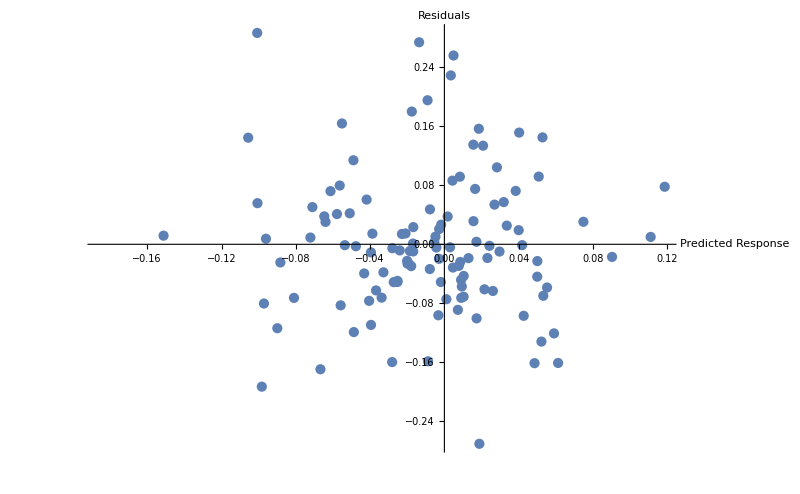

```mathematica
ListPlot[Transpose[{lmTSR["PredictedResponse"], lmTSR["FitResiduals"]}], AxesLabel->{"Predicted Response", "Residuals"}, ImageSize->800]
```

In contrast to the same plot in the cross-sectional analysis, there is no pattern. Thus, it is safe to assume, there is no heteroskedasticity and a similar transformation to the one in the cross-sectional analysis is not necessary.

#### Checking the Quantile Plot for an indication of non-normality and performing a Jarque-Bera Test

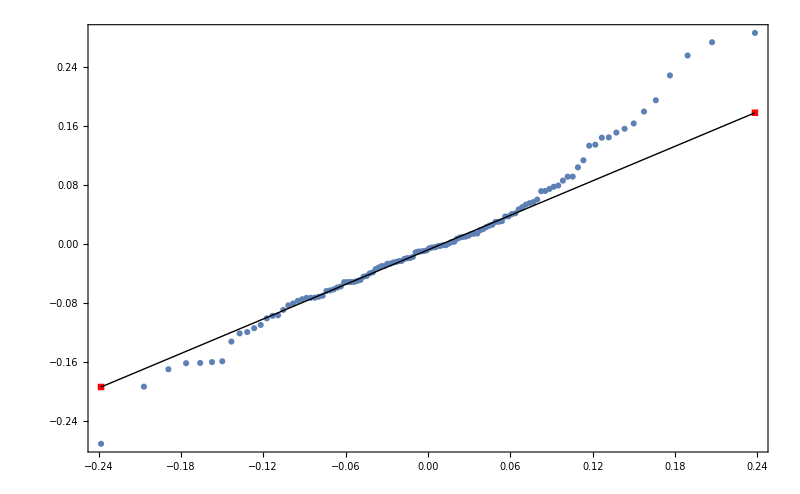

```mathematica
QuantilePlot[{lmTSR["FitResiduals"]}, PlotMarkers-> Automatic, ReferenceLineStyle->Directive[Dashing[0], Red], ImageSize->800]
```

The quantile plot indicates light tails and maybe a slight positive skew.

```mathematica
JarqueBeraALMTest[lmTSR["FitResiduals"]]
```

0.022462

At a 5% level, we can not conclude skewness and excess kurtosis to be 0.

Since, according to my notes of the statistics class regarding linear regression models, this is not an issue except for prediction bands, this is not  address this (since calculating prediction bands is not part of the analysis).

#### Timeplot of residuals and Durbin-Watson test, to test for autocorrelation

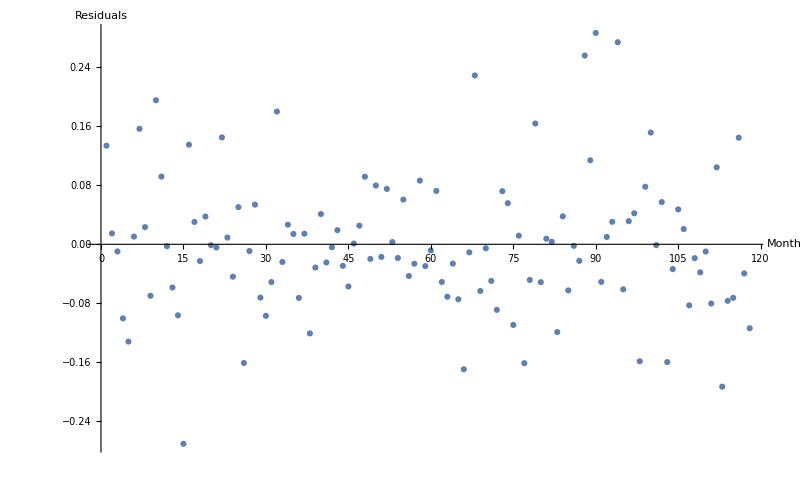

```mathematica
ListPlot[Transpose[{Normal[TimeSeriesData[All, "TimePlotDate"]], lmTSR["FitResiduals"]}], AxesLabel->{"Month", "Residuals"}, ImageSize->800, PlotMarkers->Automatic]
```

```mathematica
lmTSR["DurbinWatsonD"]
```

2.02046

Even though we are dealing with a time-series, the timeplot of the residuals does not indicate the residuals to be correlated with each other.

The Durbin-Watson test confirms that: A value between 1.5 and 2.5 means  autocorrelation to a problematic degree is not present.

#### Removing the highly insignificant Put/Call-ratio

```mathematica
lmTSRNoPC = LinearModelFit[TimeSeriesData[#&, {#Russell2000Returns, #VIX, #FederalFundsTargetRate, #SPACReturn}&]//Normal, {Russell2000Return, VIX, FederalFundsTargetRate}, {Russell2000Return, VIX, FederalFundsTargetRate}]
```

FittedModel[0.0109844-1.3238 FederalFundsTargetRate+0.837545 Russell2000Return-0.00105782 VIX]

```mathematica
lmTSRNoPC["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0109844 | 0.0302839 | 0.362714 | 0.71749
Russell2000Return | 0.837545 | 0.148779 | 5.62944 | 1.31581×10^-7
VIX | -0.00105782 | 0.0014407 | -0.734246 | 0.464307
FederalFundsTargetRate | -1.3238 | 1.20529 | -1.09832 | 0.274377

```mathematica
lmTSRNoPC["RSquared"]
```

0.238907

```mathematica
lmTSRNoPC["AdjustedRSquared"]
```

0.218878

#### Removing the highly insignificant VIX

```mathematica
lmTSRNoPCNoVIX = LinearModelFit[TimeSeriesData[#&, {#Russell2000Returns, #FederalFundsTargetRate, #SPACReturn}&]//Normal, {Russell2000Return, FederalFundsTargetRate}, {Russell2000Return, FederalFundsTargetRate}]
```

FittedModel[-0.00909004-1.16108 FederalFundsTargetRate+0.84677 Russell2000Return]

```mathematica
lmTSRNoPCNoVIX["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.00909004 | 0.0129979 | -0.699346 | 0.485748
Russell2000Return | 0.84677 | 0.14795 | 5.72334 | 8.44826×10^-8
FederalFundsTargetRate | -1.16108 | 1.18237 | -0.981999 | 0.328162

```mathematica
lmTSRNoPCNoVIX["RSquared"]
```

0.235307

```mathematica
lmTSRNoPCNoVIX["AdjustedRSquared"]
```

0.222008

## Analysis of abnormal returns

### Scatterplot

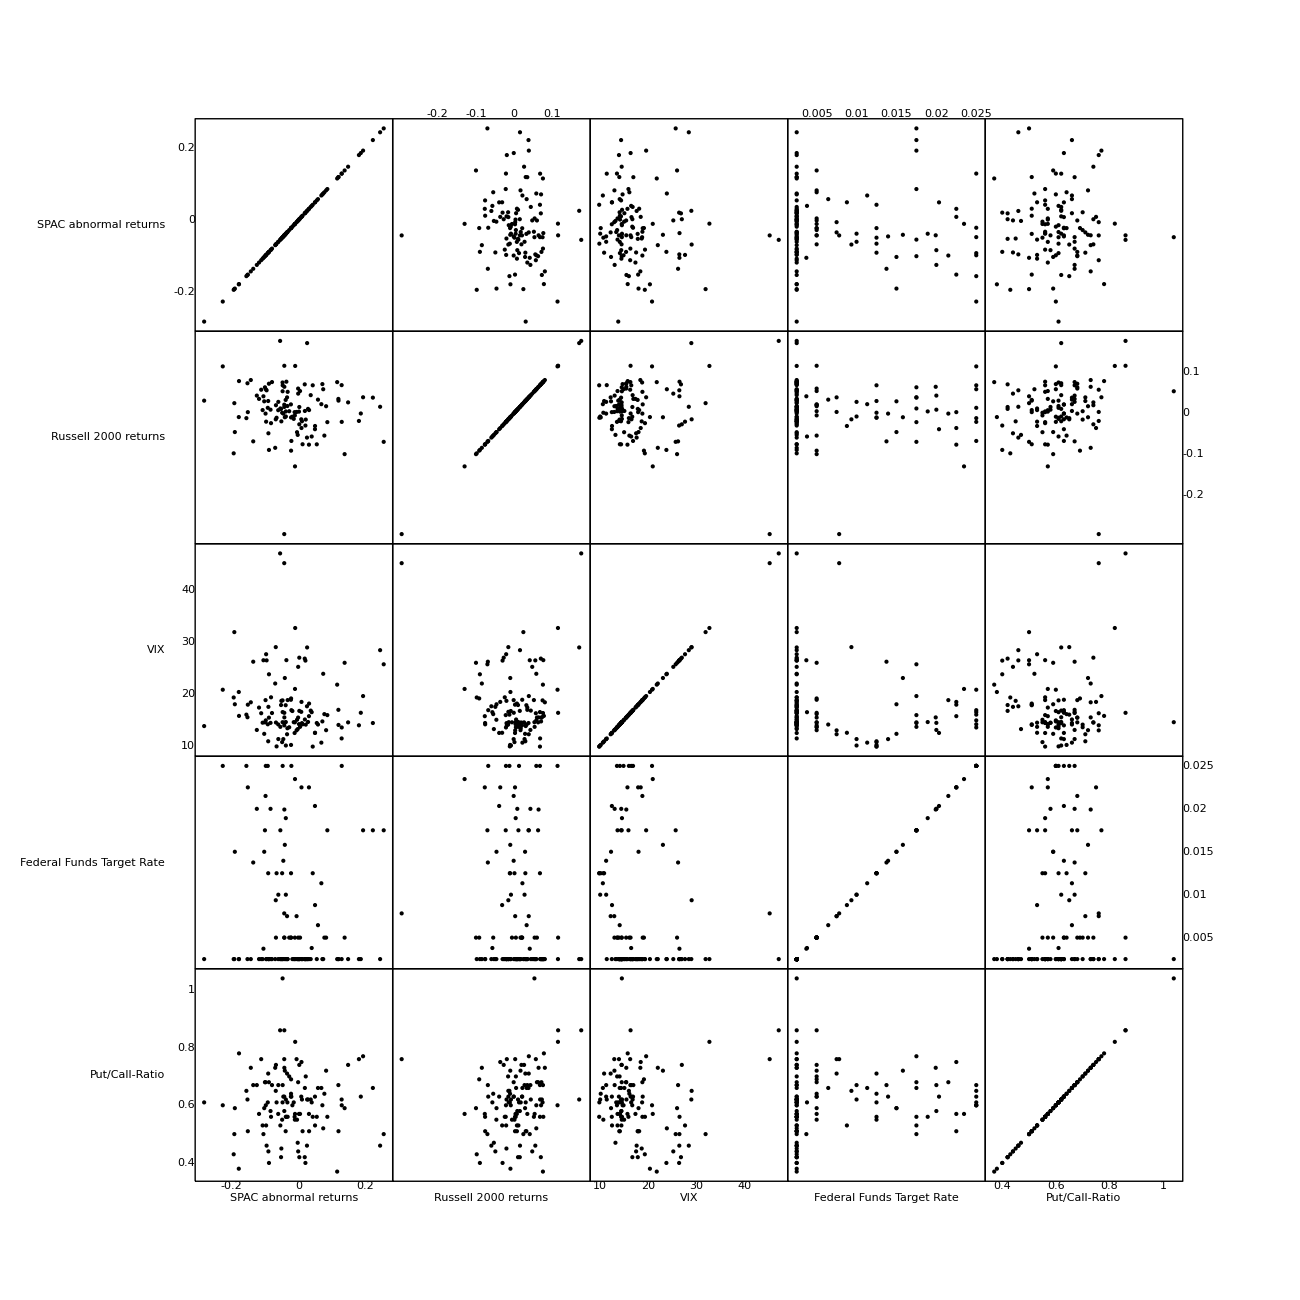

```mathematica
PairwiseScatterPlot[TimeSeriesData[#&, {#SPACAR, #Russell2000Returns, #VIX, #FederalFundsTargetRate, #PutCallRatio}&]//Normal, DataLabels->{"SPAC abnormal returns", "Russell 2000 returns", "VIX", "Federal Funds Target Rate", "Put/Call-Ratio"}, DataTicks->True, ImageSize->1300]
```

### Correlation Matrix

```mathematica
TableForm[TimeSeriesData[Correlation[#,#]&, {#SPACAR, #Russell2000Returns, #VIX, #FederalFundsTargetRate, #PutCallRatio}&]//Normal, TableHeadings->{{"SPAC abnormal returns", "Russell 2000 returns", "VIX", "Federal Funds Target Rate", "Put/Call-Ratio"},{"SPAC abnormal returns", "Russell 2000 returns", "VIX", "Federal Funds Target Rate", "Put/Call-Ratio"}}]
```

| SPAC abnormal returns | Russell 2000 returns | VIX | Federal Funds Target Rate | Put/Call-Ratio
SPAC abnormal returns | 1. | -0.0863396 | -0.0446324 | -0.0807926 | 0.00166972
Russell 2000 returns | -0.0863396 | 1. | -0.063327 | -0.110088 | 0.19665
VIX | -0.0446324 | -0.063327 | 1. | -0.17541 | -0.0372628
Federal Funds Target Rate | -0.0807926 | -0.110088 | -0.17541 | 1. | 0.129479
Put/Call-Ratio | 0.00166972 | 0.19665 | -0.0372628 | 0.129479 | 1.

### OLS Regression

```mathematica
lmTSAR = LinearModelFit[TimeSeriesData[#&, {#Russell2000Returns, #VIX, #FederalFundsTargetRate, #PutCallRatio, #SPACAR}&]//Normal, {Russell2000Return, VIX, FederalFundsTargetRate, PutCallRatio}, {Russell2000Return, VIX, FederalFundsTargetRate, PutCallRatio}]
```

FittedModel[-0.00689269-1.39175 FederalFundsTargetRate+0.0304491 PutCallRatio-0.174289 Russell2000Return-0.00105953 VIX]

```mathematica
lmTSAR//Normal
```

-0.00689269-1.39175 FederalFundsTargetRate+0.0304491 PutCallRatio-0.174289 Russell2000Return-0.00105953 VIX

```mathematica
lmTSAR["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.00689269 | 0.0579292 | -0.118985 | 0.905499
Russell2000Return | -0.174289 | 0.152875 | -1.14008 | 0.256665
VIX | -0.00105953 | 0.00144622 | -0.732619 | 0.465308
FederalFundsTargetRate | -1.39175 | 1.22434 | -1.13673 | 0.258055
PutCallRatio | 0.0304491 | 0.0839901 | 0.362533 | 0.717631

### Goodness of Fit

```mathematica
lmTSAR["RSquared"]
```

0.0214792

```mathematica
lmTSAR["AdjustedRSquared"]
```

-0.0131587

### Checking Scatterplot with the linear models predicted response on the x-axis and the residuals of the y-axis for a pattern which may indicate the presence of heteroskedasticity

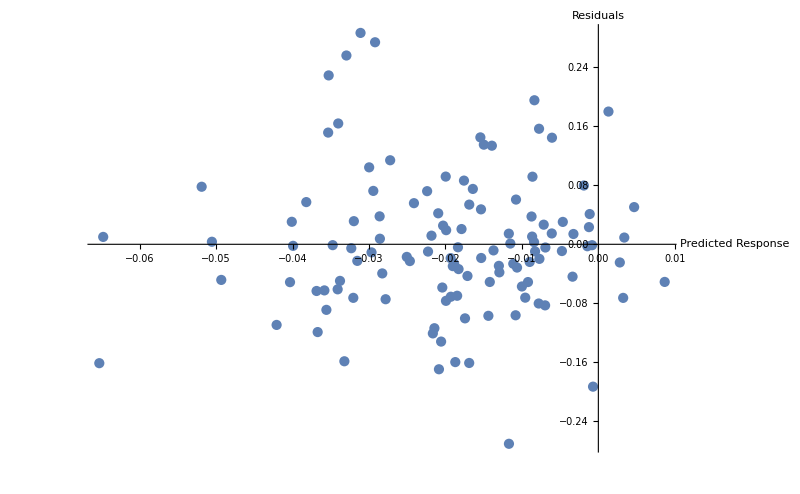

```mathematica
ListPlot[Transpose[{lmTSAR["PredictedResponse"], lmTSAR["FitResiduals"]}], AxesLabel->{"Predicted Response", "Residuals"}, ImageSize->800]
```

no pattern indicating any problems is present

#### Checking the Quantile Plot for an indication of non-normality and performing a Jarque-Bera Test

```mathematica
QuantilePlot[{lmTSAR["FitResiduals"]}, PlotMarkers-> Automatic, ReferenceLineStyle->Directive[Dashing[0], Red], ImageSize->800]
```

-Graphics-

```mathematica
JarqueBeraALMTest[lmTSAR["FitResiduals"]]
```

0.022462

Just like with absolute returns, the quantile plot indicates light tails and maybe a slight positive right skew.

Again not an issue since no prediction bands will be calculated.

#### Timeplot of residuals and Durbin-Watson test, to test for autocorrelation

```mathematica
ListPlot[Transpose[{Normal[TimeSeriesData[All, "TimePlotDate"]], lmTSAR["FitResiduals"]}], AxesLabel->{"Month", "Residuals"}, ImageSize->800, PlotMarkers->Automatic]
```

-Graphics-

```mathematica
lmTSAR["DurbinWatsonD"]
```

2.02046

Autocorrelation is not an issue

#### Removing the Put/Call-ratio

```mathematica
lmTSARNoPC = LinearModelFit[TimeSeriesData[#&, {#Russell2000Returns, #VIX, #FederalFundsTargetRate, #SPACAR}&]//Normal, {Russell2000Return, VIX, FederalFundsTargetRate}, {Russell2000Return, VIX, FederalFundsTargetRate}]
```

FittedModel[0.0109844-1.3238 FederalFundsTargetRate-0.162455 Russell2000Return-0.00105782 VIX]

```mathematica
lmTSARNoPC["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0109844 | 0.0302839 | 0.362714 | 0.71749
Russell2000Return | -0.162455 | 0.148779 | -1.09192 | 0.27717
VIX | -0.00105782 | 0.0014407 | -0.734246 | 0.464307
FederalFundsTargetRate | -1.3238 | 1.20529 | -1.09832 | 0.274377

```mathematica
lmTSARNoPC["RSquared"]
```

0.0203411

```mathematica
lmTSARNoPC["AdjustedRSquared"]
```

-0.00543939

#### Removing the VIX

```mathematica
lmTSARNoPCNoVIX = LinearModelFit[TimeSeriesData[#&, {#Russell2000Returns, #FederalFundsTargetRate, #SPACAR}&]//Normal, {Russell2000Return, FederalFundsTargetRate}, {Russell2000Return, FederalFundsTargetRate}]
```

FittedModel[-0.00909004-1.16108 FederalFundsTargetRate-0.15323 Russell2000Return]

```mathematica
lmTSARNoPCNoVIX["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.00909004 | 0.0129979 | -0.699346 | 0.485748
Russell2000Return | -0.15323 | 0.14795 | -1.03568 | 0.302523
FederalFundsTargetRate | -1.16108 | 1.18237 | -0.981999 | 0.328162

```mathematica
lmTSARNoPCNoVIX["RSquared"]
```

0.0157082

```mathematica
lmTSARNoPCNoVIX["AdjustedRSquared"]
```

-0.00140991

#### Removing the Federal Funds Rate

```mathematica
lmTSARFinal = LinearModelFit[TimeSeriesData[#&, {#Russell2000Returns, #SPACAR}&]//Normal, Russell2000Return, Russell2000Return]
```

FittedModel[-0.0183629-0.137235 Russell2000Return]

```mathematica
lmTSARFinal["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0183629 | 0.00893048 | -2.05621 | 0.042006
Russell2000Return | -0.137235 | 0.147029 | -0.933391 | 0.352557

```mathematica
lmTSARFinal["RSquared"]
```

0.00745453

```mathematica
lmTSARFinal["AdjustedRSquared"]
```

-0.0011019

Definitely non of the variables are significant at any level